# Project 1 | Bachelors’ Degrees

## Data:

```mathematica
year = {1998, 1999, 2000, 2001, 2002, 2003, 2004, 2005, 2006, 2007, 2008, 2009};
```

```mathematica
degrees ={664,682,708,712,742, 776, 804, 826, 855, 875, 895, 916};
```

### Project Parameters:

The source of this project comes from the website comes from Ron Larson’s pre-calculus textbook website. More specifically, this project comes from Larson’s Pre-calculus with Limits 3rd edition website.

Using the data given by the  project’s parameters, I will analyse the given data set using the given formula:

	B = 23.96t + 464.4, 8 ≤ t ≤ 19
	
where t represent the year, with t = 8 corresponding to 1998 and B refers to the number (in thousands ) of bachelors degrees earned by women in the United Stats from 1998 o 2009.

The data points that are given come from the U.S. Census Bureau. 

The purpose of this project to estimate the growth of bachelor’s degrees earned by women.

### Project Objectives :

a) Construct a table using the given data sets.
b)  Use Mathematica to plot the data and graph the model in the same  viewing window.
c) Use the model to approximate the number of bachelor’s degrees earned by women for each year from 1998 through 2009.

d) Compare the estimated to the actual data. is the model a good fit for the data? Explain your reasoning.
e)  What are the slope and y-intercept of the model? Interpret their meaning in the context of the problem.
f) Use the model to predict the number of bachelor’s degrees earned by women in 2015.

#### a) Data Table:

```mathematica
dtable= Transpose[{year,degrees}];
colHeadings = {"Year", " Actual Bachelor's Degrees,B"};
```

```mathematica
table1 =TableForm[dtable, TableHeadings->{None,colHeadings},TableAlignments->{Center, Center}];
```

```mathematica
table1
```

Year |  Actual Bachelor's Degrees,B
1998 | 664
1999 | 682
2000 | 708
2001 | 712
2002 | 742
2003 | 776
2004 | 804
2005 | 826
2006 | 855
2007 | 875
2008 | 895
2009 | 916

#### b) Data Plot

We need create a new list in the and then use the ListLinePlot function to create the graph.

```mathematica
timedata1 = {{1998,664},{1999,682},{2000,708},{2001,712},{2002,742},{2003,776},{2004,804},{2005,826},{2006,855},{2007,875},{2008,895},{2009,916}};
```

```mathematica
plot1 = ListLinePlot[timedata1,AxesLabel->{"Year","Bachelor"},LabelStyle->{"Times New Roman",10,GrayLevel[0],Bold},PlotLabel->"Acutal",PlotStyle->Blue];
```

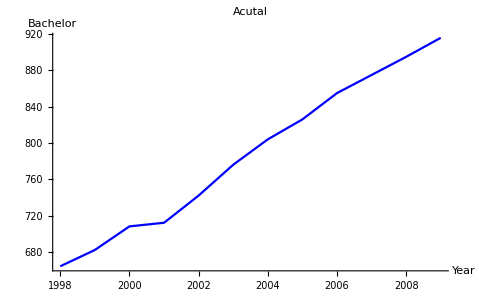

```mathematica
Show[plot1]
```

#### c) Approximation

For this part of the project we need to create the function given by the project parameters and use the domain given by that project to approximate the number of degrees earned by women in the given years.

```mathematica
Clear[B,t]
```

```mathematica
B[t_] :=23.96t + 464.4
```

Estimating for t = 8

```mathematica
B[8]
```

656.08

Estimating for t = 9

```mathematica
B[9]
```

680.04

Estimating for t = 10

```mathematica
B[10]
```

704.

Estimating for t =11

```mathematica
B[11]
```

727.96

Estimating for t = 12

```mathematica
B[12]
```

751.92

Estimating for t = 13

```mathematica
B[13]
```

775.88

Estimating for t = 14

```mathematica
B[14]
```

799.84

Estimating for t = 15

```mathematica
B[15]
```

823.8

Estimating for t = 16

```mathematica
B[16]
```

847.76

Estimating for t = 17

```mathematica
B[17]
```

871.72

Estimating for t = 18

```mathematica
B[18]
```

895.68

Estimating for t = 19

```mathematica
B[19]
```

919.64

#### d) Comparison: Actual vs. Approximation

For the comparison portion of this project, I will create a table and plot of the approximation of the given dataset and compare it with the actual data.

```mathematica
t= {8,9,10,11,12,13,14,15,16,17,18,19};
approx = {656.08, 680.04, 704,727.96,751.92,775.88,799.84,823.80,847.76,871.72,895.68,919.64};
```

```mathematica
dtable2 = Transpose[{t,approx}];
```

```mathematica
colHeadings1 = {"t", " Apporximation Bachelor's Degrees,B"};
```

```mathematica
table2 = TableForm[dtable2,TableHeadings->{None, colHeadings1},TableAlignments->{Center, Center}];
```

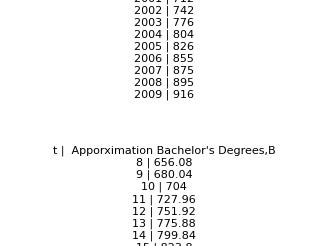

```mathematica
GraphicsGrid[{{table1},{table2}}]
```

Notice that the differences in the outputs from the actual data vs the approximation in small. There are no large dispersions between the actual data and the approximation that we received from the function

 B = 23.96t + 464.4, 8 ≤ t ≤ 19
 
 This means that the above function is a good fit for the actual data because the outputs that it gives us for the estimation of the data is not very disperse.

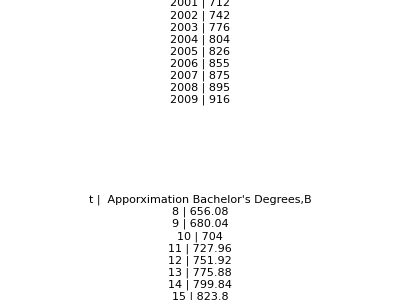

To create a second plot that contains the outcomes from the model I created a new list that contains the inputs and outputs from the model.

I will then place it side by side with plot of the actual data to make comparisons.

```mathematica
timedata2 = {{8,656.08},{9,680.04},{10,704},{11,727.96},{12,751},{13,775.88},{14,799.84},{15,823.80},{16,847.76},{17,871.72},{18,895.68},{19,919.64}};
```

```mathematica
plot2 =ListLinePlot[timedata2,AxesLabel->{"t","Bachelor"},LabelStyle->{"Times New Roman",10,GrayLevel[0],Bold},PlotLabel->"Approximation ",PlotStyle->Blue];
```

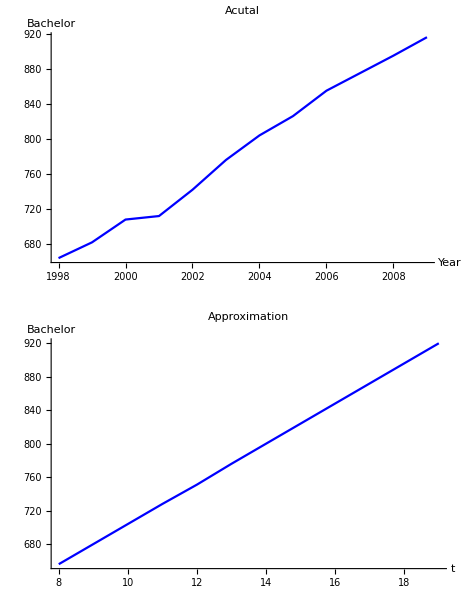

```mathematica
GraphicsGrid[{{plot1},{plot2}}]
```

Please note that the actual plot is generally moving in a linear direction with the exception of the 1998 to 2000 timespan indicating that the number of women earning bachelors degrees is increasing at roughly the same pace. Note that the approximation  plot is completely linear. The comparison of the two graphs proves that the model is a good fit for the actual data because it mirrors the actual data with  exception of the first two years.

#### e) The Slope and the Interception

We have 
		B = 23.96t + 464.4, 8 ≤ t ≤ 19,
		
The slope is m = 23.96 and the y-intercept is 464.4. By definition, the slope is the direction and the steepness of the line. In this context, the slope describe the rate of change of how many women will earned bachelor’s degrees. The number 23.96 describe the rate of growth of how many women will earned bachelor’s degrees during a given time period. The y-intercept is the fixed point on the y-axis of a graph. In this case, the number 464.4 is a fixed value of women who had earned a bachelor’s degree.

#### f) Prediction

In this case we are asked to predict what will be the number of women who will earned a bachelor’s degree in 2015.

```mathematica
B[25]
```

1063.4

According to the model we will have 1,063.4 women who will earn a bachelor’s degree in 2015.